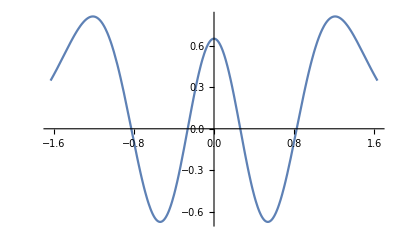

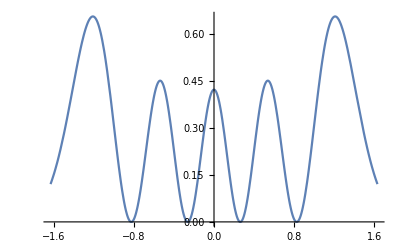

```mathematica
ℏ = 1;
m=16;
k=1;
n=4;
α= ((m*k)/ℏ^2)^(1/4);
ε= α*x;
ψ[x_]:= ⅇ^(-ε^2/2) *HermiteH[n,ε]*(α/(√π*(2^n)*n!))^(1/2)
Plot[ψ[x],{x,-1.63124,1.63124}]
Plot[Abs[ψ[x]]^2,{x,-1.63124,1.63124}]
```